## Clear

```mathematica
Button["Clear",
{Clear [A,A1,A2,B,B1,B2,AA,AA1,AA2,BB,BB1,BB2,a,b,aa,bb,v,T0,V0,theta,x0,x0max,h,temp,w,Amax,Bmax,AAmax,BBmax,amax,bmax,aamax,bbmax,x0max,hmax,V0,T0,xmin,xmax,ymin,ymax,Xmin,Xmax,Ymin,Ymax]
}]
```

Clear

## Expressions

```mathematica
A0=A/a;
B0=B/b;
AA0=AA/aa;
BB0=BB/bb;
A1[v_]:=(A/(a*(a-1/v)));
B1[v_]:=(B/(b*(b-1/v)));
A2[v_]:=(A/(a*(a+1/v)));
B2[v_]:=(B/(b*(b+1/v)));
AA1[v_]:=(AA/(aa*(aa-1/v)));
BB1[v_]:=(BB/(bb*(bb-1/v)));
AA2[v_]:=(AA/(aa*(aa+1/v)));
BB2[v_]:=(BB/(bb*(bb+1/v)));

a1[theta_]:=1-Exp[a*theta];
b1[theta_]:=1-Exp[b*theta];
aa1[theta_]:=Exp[aa*x0]-Exp[aa*(theta+x0)];
bb1[theta_]:=Exp[bb*x0]-Exp[bb*(theta+x0)];

Amax = 10;
Bmax = 10;
AAmax = 10;
BBmax = 10;
x0max = 10;
amax = 1;
bmax = 1;
aamax = 1;
bbmax = 1;
hmax = 10;
```

## System

```mathematica
V0=10;T0=12; (*large, stable*)
(*V0=12; T0=8;*) (*small, unstable*)
```

```mathematica
Manipulate[
global = {A,B,AA,BB,a,b,aa,bb,x0,h};
ContourPlot[{
h-(1/v)*
(
(A/(a*(a-1/v)))*(Exp[-a*theta]-Exp[-theta/v])-(B/(b*(b-1/v)))*(Exp[-b*theta]-Exp[-theta/v])+
(AA/(aa*(aa-1/v)))*(Exp[-aa*x0]*(Exp[-aa*theta]-1)+Exp[-x0/v]*(1-Exp[-theta/v]))-(BB/(bb*(bb-1/v)))*(Exp[-bb*x0]*(Exp[-bb*theta]-1)+Exp[-x0/v]*(1-Exp[-theta/v]))+2*v*(1-Exp[-theta/v])*(A/a-B/b+Exp[-x0/v]*(AA/aa-BB/bb))+(Exp[-theta/v]-1)*((A/(a*(a+1/v)))-(B/(b*(b+1/v)))+Exp[-x0/v]*((AA/(aa*(aa+1/v)))-(BB/(bb*(bb+1/v)))))
)==0,

(*x0<theta*)
-h+Exp[theta/v]*
(
h-(1/v)*
(
(A/(a*(a-1/v)))*(Exp[-a*theta]-Exp[-theta/v])-(B/(b*(b-1/v)))*(Exp[-b*theta]-Exp[-theta/v])+
(AA/(aa*(aa-1/v)))*(Exp[-x0/v]-Exp[-aa*x0]*(1+Exp[-theta/v]-Exp[-aa*theta]))-
(BB/(bb*(bb-1/v)))*(Exp[-x0/v]-Exp[-bb*x0]*(1+Exp[-theta/v]-Exp[-bb*theta]))-2*v*((A/a-B/b)*(Exp[-theta/v]-1)+(AA/aa-BB/bb)*(Exp[-theta/v]-Exp[-x0/v]))+(A/(a*(a+1/v)))*(Exp[-a*theta-theta/v]-1)-(B/(b*(b+1/v)))*(Exp[-b*theta-theta/v]-1)+(AA/(aa*(aa+1/v)))*(Exp[aa*x0-aa*theta-theta/v]-Exp[-x0/v])-(BB/(bb*(bb+1/v)))*(Exp[bb*x0-bb*theta-theta/v]-Exp[-x0/v])
)
)==0,

theta-x0==0


},{v,0,30},{theta,0,30},ContourShading->None,FrameLabel->{"v","width"}
]
,{A,0,Amax},{a,0.0001,amax},{B,0,Bmax},{b,0.0001,bmax},{AA,0,AAmax},{aa,0.0001,aamax},{BB,0,BBmax},{bb,0.0001,bbmax},{x0,0,x0max},{h,0,hmax}]

Button["Save Parameters",
{A =Setting[Dynamic[global[[1]]]],
B=Setting[Dynamic[global[[2]]]],
AA =Setting[Dynamic[global[[3]]]],
BB=Setting[Dynamic[global[[4]]]],
a =Setting[Dynamic[global[[5]]]],
b =Setting[Dynamic[global[[6]]]],
aa =Setting[Dynamic[global[[7]]]],
bb =Setting[Dynamic[global[[8]]]],
x0 =Setting[Dynamic[global[[9]]]],
h =Setting[Dynamic[global[[10]]]]
}]
```

Save Parameters

## Kernel

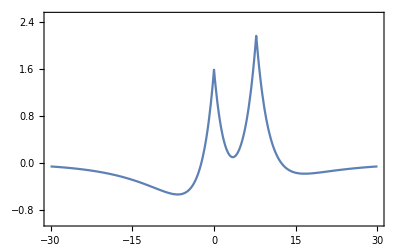

```mathematica
Plot[A*Exp[-a*Abs[x]]-B*Exp[-b*Abs[x]]+AA*Exp[-aa*Abs[x-x0]]-BB*Exp[-bb*Abs[x-x0]],{x,-30,30},PlotRange->{-1,2.5},Frame->True]
```

## Solution

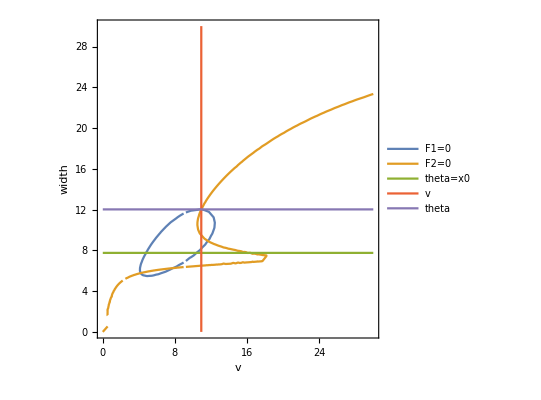

V=

10.9227222382222066698886919767

T=

12.0175966699383423019753536209

```mathematica
F1=h-(1/v)*
(
2*(1-Exp[-theta/v])*v*(A0-B0+Exp[-x0/v]*(AA0-BB0))+
A1[v]*(Exp[-a*theta]-Exp[-theta/v])-
B1[v]*(Exp[-b*theta]-Exp[-theta/v])+
AA1[v]*(Exp[-aa*x0]*(Exp[-aa*theta]-1)+Exp[-x0/v]*(1-Exp[-theta/v]))-
BB1[v]*(Exp[-bb*x0]*(Exp[-bb*theta]-1)+Exp[-x0/v]*(1-Exp[-theta/v]))+
(Exp[-theta/v]-1)*(A2[v]-B2[v]+Exp[-x0/v]*(AA2[v]-BB2[v]))
);

F2=-h+Exp[theta/v]*
(
h-(1/v)*
(
2*v*((A0-B0)*(1-Exp[-theta/v])+(AA0-BB0)*(Exp[-x0/v]-Exp[-theta/v]))+
A1[v]*(Exp[-a*theta]-Exp[-theta/v])-
B1[v]*(Exp[-b*theta]-Exp[-theta/v])+
AA1[v]*(Exp[-x0/v]-Exp[-aa*x0]*(1+Exp[-theta/v]-Exp[-aa*theta]))-
BB1[v]*(Exp[-x0/v]-Exp[-bb*x0]*(1+Exp[-theta/v]-Exp[-bb*theta]))+
A2[v]*(Exp[-theta*(a+1/v)]-1)-
B2[v]*(Exp[-theta*(b+1/v)]-1)+
AA2[v]*(Exp[aa*x0]*Exp[-theta*(aa+1/v)]-Exp[-x0/v])-
BB2[v]*(Exp[bb*x0]*Exp[-theta*(bb+1/v)]-Exp[-x0/v])
)
);

sol1=SetPrecision[ FindRoot[{F1==0,F2==0},{v,V0},{theta,T0}],30];
v1=v/.sol1[[1]];
theta1=theta/.sol1[[2]];
vv=v1;
th=theta1;

ContourPlot[{F1==0,F2==0,theta==x0,v==vv,theta==th},{v,0,30},{theta,0,30},ContourShading->None,PlotLegends->{"F1=0","F2=0","theta=x0","v","theta"}, FrameLabel->{"v","width"}]

Print["V="]
vv
Print["T="]
th
```

## Pulse

```mathematica
(*bump plot range*)
xmin = -50;
xmax = 50;
ymin = -02;
ymax = 6;
```

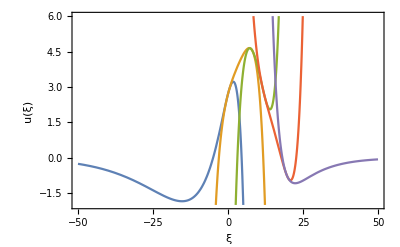

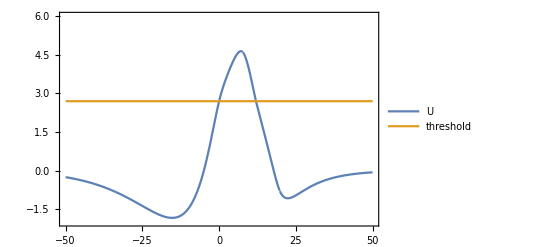

Max Error=

2.57572×10^-14

```mathematica
integral1[x_]:=
A1[vv]*(1-Exp[-a*th])*(Exp[x*(a-1/vv)]-1)-B1[vv]*(1-Exp[-b*th])*(Exp[x*(b-1/vv)]-1)+
AA1[vv]*Exp[-aa*x0]*(1-Exp[-aa*th])*(Exp[x*(aa-1/vv)]-1)-
BB1[vv]*Exp[-bb*x0]*(1-Exp[-bb*th])*(Exp[x*(bb-1/vv)]-1)

integral2[x_]:=
2*(A0-B0)*vv*(1-Exp[-x/vv])+
A1[vv]*Exp[-a*th]*(1-Exp[x*(a-1/vv)])-
B1[vv]*Exp[-b*th]*(1-Exp[x*(b-1/vv)])+
AA1[vv]*Exp[-aa*x0]*(Exp[-aa*th]-1)*(1-Exp[x*(aa-1/vv)])-
BB1[vv]*Exp[-bb*x0]*(Exp[-bb*th]-1)*(1-Exp[x*(bb-1/vv)])+
A2[vv]*(Exp[-x*(a+1/vv)]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]-1)

integral3a[x_]:=
2*(A0-B0)*vv*(1-Exp[-x/vv])+
2*(AA0-BB0)*vv*(Exp[-x0/vv]-Exp[-x/vv])+
A1[vv]*Exp[-a*th]*(1-Exp[x*(a-1/vv)])-
B1[vv]*Exp[-b*th]*(1-Exp[x*(b-1/vv)])+
AA1[vv]*(Exp[-aa*(th+x0)]*(1-Exp[x*(aa-1/vv)])+Exp[-x0/vv]-Exp[-aa*x0])-
BB1[vv]*(Exp[-bb*(th+x0)]*(1-Exp[x*(bb-1/vv)])+Exp[-x0/vv]-Exp[-bb*x0])+
A2[vv]*(Exp[-x*(a+1/vv)]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]-1)+
AA2[vv]*(Exp[aa*x0]*Exp[-x*(aa+1/vv)]-Exp[-x0/vv])-
BB2[vv]*(Exp[bb*x0]*Exp[-x*(bb+1/vv)]-Exp[-x0/vv])

integral3b[x_]:=
2*(A0-B0)*vv*(1-Exp[-th/vv])+
A1[vv]*(Exp[-a*th]-Exp[-th/vv])-
B1[vv]*(Exp[-b*th]-Exp[-th/vv])+
AA1[vv]*Exp[-aa*x0]*(Exp[-aa*th]-1)*(1-Exp[x*(aa-1/vv)])-
BB1[vv]*Exp[-bb*x0]*(Exp[-bb*th]-1)*(1-Exp[x*(bb-1/vv)])+
A2[vv]*(Exp[-x*(a+1/vv)]*(1-Exp[a*th])+Exp[-th/vv]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]*(1-Exp[b*th])+Exp[-th/vv]-1)

integral3[x_]:=If[x0<th,integral3a[x],integral3b[x]]

integral4[x_]:=
2*(A0-B0)*vv*(1-Exp[-th/vv])+
2*(AA0-BB0)*vv*(Exp[-x0/vv]-Exp[-x/vv])+
A1[vv]*(Exp[-a*th]-Exp[-th/vv])-
B1[vv]*(Exp[-b*th]-Exp[-th/vv])+
AA1[vv]*(Exp[-aa*(th+x0)]*(1-Exp[x*(aa-1/vv)])+Exp[-x0/vv]-Exp[-aa*x0])-
BB1[vv]*(Exp[-bb*(th+x0)]*(1-Exp[x*(bb-1/vv)])+Exp[-x0/vv]-Exp[-bb*x0])+
A2[vv]*(Exp[-x*(a+1/vv)]*(1-Exp[a*th])+Exp[-th/vv]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]*(1-Exp[b*th])+Exp[-th/vv]-1)+
AA2[vv]*(Exp[aa*x0]*Exp[-x*(aa+1/vv)]-Exp[-x0/vv])-
BB2[vv]*(Exp[bb*x0]*Exp[-x*(bb+1/vv)]-Exp[-x0/vv])

integral5[x_]:=
2*(A0-B0)*vv*(1-Exp[-th/vv])+
2*(AA0-BB0)*vv*(Exp[-x0/vv]-Exp[-(th+x0)/vv])+
A1[vv]*(Exp[-a*th]-Exp[-th/vv])-
B1[vv]*(Exp[-b*th]-Exp[-th/vv])+
AA1[vv]*(Exp[-x0/vv]*(1-Exp[-th/vv])-Exp[-aa*x0]*(1-Exp[-aa*th]))-
BB1[vv]*(Exp[-x0/vv]*(1-Exp[-th/vv])-Exp[-bb*x0]*(1-Exp[-bb*th]))+
A2[vv]*(Exp[-x*(a+1/vv)]*(1-Exp[a*th])+Exp[-th/vv]-1)-
B2[vv]*(Exp[-x*(b+1/vv)]*(1-Exp[b*th])+Exp[-th/vv]-1)+
AA2[vv]*(Exp[-x*(aa+1/vv)]*(Exp[aa*x0]-Exp[aa*(th+x0)])+Exp[-(th+x0)/vv]-Exp[-x0/vv])-
BB2[vv]*(Exp[-x*(bb+1/vv)]*(Exp[bb*x0]-Exp[bb*(th+x0)])+Exp[-(th+x0)/vv]-Exp[-x0/vv])

curve1[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral1[x]
curve2[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral2[x]
curve3[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral3[x]
curve4[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral4[x]
curve5[x_]:=h*Exp[x/vv]-(1/vv)*Exp[x/vv]*integral5[x]
u5[x_]:=-(1/vv)*(a1[th]*A2[vv]*Exp[-x*a]-b1[th]*B2[vv]*Exp[-x*b]+aa1[th]*AA2[vv]*Exp[-x*aa]-bb1[th]*BB2[vv]*Exp[-x*bb])
travbump[x_]:=Piecewise[{
{curve1[x],x<=0},
{curve2[x],0<x<=Min[x0,th]},
{curve3[x],Min[x0,th]<x<=Max[x0,th]},
{curve4[x],Max[x0,th]<x<=x0+th},
{u5[x],x0+th<x}
}]
travbump2[x_]:=Piecewise[{
{curve1[x],x<=0},
{curve2[x],0<x<=Min[x0,th]},
{curve3[x],Min[x0,th]<x<=Max[x0,th]},
{curve4[x],Max[x0,th]<x<=x0+th},
{curve5[x],x0+th<x<Infinity}
}]

Plot[{curve1[x],curve2[x],curve3[x],curve4[x],curve5[x]},{x,xmin,xmax},PlotRange->{ymin,ymax},Frame->True,Axes->None,FrameLabel->{ξ,"u(ξ)"}]
Plot[{travbump[x],h},{x,xmin,xmax},PlotLegends->{"U","threshold"},PlotRange->{ymin,ymax},Frame->True]
Plot[{travbump2[x],h},{x,xmin,xmax},PlotLegends->{"U","threshold"},PlotRange->ymax];

errors = {Abs[curve1[0]-h],Abs[curve2[0]-h],Abs[curve2[x0]-curve3[x0]],Abs[curve3[th]-h],Abs[curve4[th]-h],Abs[curve4[x0+th]-curve5[x0+th]]};

Print ["Max Error="]
Max[errors]
```

```mathematica
(*evans function plot range*)
Xmin = -10;
Xmax = 2;
Ymin = -12;
Ymax = 12;

lambdaX = 1;
lambdaY = 0;
```

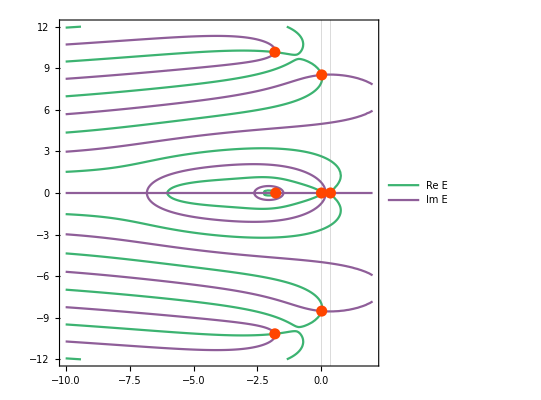

Positive Eigenvalue?=

0.35394979655231095794221118922

```mathematica
W1[x_]:=A0*Exp[a*x]*(1-Exp[-a*th])-B0*Exp[b*x]*(1-Exp[-b*th])+AA0*Exp[aa*(x-x0)]*(1-Exp[-aa*th])-BB0*Exp[bb*(x-x0)]*(1-Exp[-bb*th]);
W2[x_]:=2*A0-A0*(Exp[a*(x-th)]+Exp[-a*x])-2*B0+B0*(Exp[b*(x-th)]+Exp[-b*x])+AA0*Exp[aa*(x-x0)]*(1-Exp[-aa*th])-BB0*Exp[bb*(x-x0)]*(1-Exp[-bb*th]);
W3[x_]:=2*(A0-B0)-A0*(Exp[a*(x-th)]+Exp[-a*x])+B0*(Exp[b*(x-th)]+Exp[-b*x])+2*(AA0-BB0)-AA0*(Exp[aa*(x-th-x0)]+Exp[-aa*(x-x0)])+BB0*(Exp[bb*(x-th-x0)]+Exp[-bb*(x-x0)]);
W4[x_]:=A0*Exp[-a*x]*(Exp[a*th]-1)-B0*Exp[-b*x]*(Exp[b*th]-1)+2*(AA0-BB0)-AA0*(Exp[aa*(x-th-x0)]+Exp[-aa*(x-x0)])+BB0*(Exp[bb*(x-th-x0)]+Exp[-bb*(x-x0)]);
W5[x_]:=A0*Exp[-a*x]*(Exp[a*th]-1)-B0*Exp[-b*x]*(Exp[b*th]-1)+AA0*Exp[-aa*(x-x0)]*(Exp[aa*th]-1)-BB0*Exp[-bb*(x-x0)]*(Exp[bb*th]-1);
W[x_]:=Piecewise[{{W1[x],x<0},{W2[x],0≤x<x0},{W3[x],x0<=x<th},{W4[x],th≤x<x0+th},{W5[x],x≥x0+th}}]

K0=1/Abs[h-W[0]];
Kth=1/Abs[h-W[th]];

G1[x_,l_]:=A*vv/(a*vv-l-1)*(Exp[(l+1)*x/vv]-Exp[a*x])+A*vv/(a*vv+l+1)*Exp[(l+1)*x/vv]-B*vv/(b*vv-l-1)*(Exp[(l+1)*x/vv]-Exp[b*x])-B*vv/(b*vv+l+1)*Exp[(l+1)*x/vv]+AA*vv/(aa*vv-l-1)*(Exp[(l+1)/vv*(x-x0)]-Exp[aa*(x-x0)])+AA*vv/(aa*vv+l+1)*Exp[(l+1)/vv*(x-x0)]-BB*vv/(bb*vv-l-1)*(Exp[(l+1)/vv*(x-x0)]-Exp[bb*(x-x0)])-BB*vv/(bb*vv+l+1)*Exp[(l+1)/vv*(x-x0)];
G2[x_,l_]:=A*vv/(a*vv+l+1)*Exp[-a*x]-B*vv/(b*vv+l+1)*Exp[-b*x]+AA*vv/(aa*vv-l-1)*(Exp[(l+1)/vv*(x-x0)]-Exp[aa*(x-x0)])+AA*vv/(aa*vv+l+1)*Exp[(l+1)/vv*(x-x0)]-BB*vv/(bb*vv-l-1)*(Exp[(l+1)/vv*(x-x0)]-Exp[bb*(x-x0)])-BB*vv/(bb*vv+l+1)*Exp[(l+1)/vv*(x-x0)];
G3[x_,l_]:=A*vv/(a*vv+l+1)*Exp[-a*x]-B*vv/(b*vv+l+1)*Exp[-b*x]+AA*vv/(aa*vv+l+1)*Exp[-aa*(x-x0)]-BB*vv/(bb*vv+l+1)*Exp[-bb*(x-x0)];
G[x_,l_]:=Piecewise[{{G1[x,l],x<0},{G2[x,l],0≤x<x0},{G3[x,l],x≥x0}}];

Ev[l_]:=(K0*G[0,l]-1)*(Kth*G[0,l]-1)-K0*Kth*G[th,l]*G[-th,l];

Options[FindRoots2D]={PlotPoints->Automatic,MaxRecursion->Automatic};

FindRoots2D[funcs_,{x_,a_,b_},{y_,c_,d_},opts___]:=Module[{fZero,seeds,signs,fy},fy=Compile[{x,y},Evaluate[funcs[[2]]]];
fZero=Cases[Normal[ContourPlot[funcs[[1]]==0,{x,a-(b-a)/97,b+(b-a)/103},{y,c-(d-c)/98,d+(d-c)/102},Evaluate[FilterRules[{opts},Options[ContourPlot]]]]],Line[z_]:>z,Infinity];
seeds=Flatten[((signs=Sign[Apply[fy,#1,{1}]];
#1[[1+Flatten[Position[Rest[signs*RotateRight[signs]],-1]]]])&)/@fZero,1];
If[seeds=={},{},Select[Union[({x,y}/.FindRoot[{funcs[[1]],funcs[[2]]},{x,#1[[1]]},{y,#1[[2]]},Evaluate[FilterRules[{opts},Options[FindRoot]]]]&)/@seeds,SameTest->(Norm[#1-#2]<10^(-6)&)],a≤#1[[1]]≤b&&c≤#1[[2]]≤d&]]]

zeros=FindRoots2D[{Re[Ev[x+I y]],Im[Ev[x+I y]]},{x,-4,12},{y,-12,12}];

mediumSeaGreen=RGBColor[0.235298,0.702002,0.443098];
violet=RGBColor[0.559999,0.370006,0.599994];
orangeRed=RGBColor[1.,0.270608,0.];

Lambda=SetPrecision[ FindRoot[{Re[Ev[x+I y]]==0,Im[Ev[x+I y]]==0},{x,lambdaX},{y,lambdaY}],30];
reLambda=x/.Lambda[[1]];
imLambda=y/.Lambda[[2]];

ContourPlot[{Re[Ev[x+I y]]==0,Im[Ev[x+I y]]==0},{x,Xmin,Xmax},{y,Ymin,Ymax},MaxRecursion->3,GridLines->{{0,reLambda},{}},ContourStyle->{Directive[Thick,mediumSeaGreen],Directive[Thick,violet]},Epilog->{PointSize[0.02],orangeRed,Point[zeros]},PlotLegends->{"Re E","Im E"}]

Print["Positive Eigenvalue?="];
reLambda+ I*imLambda
```

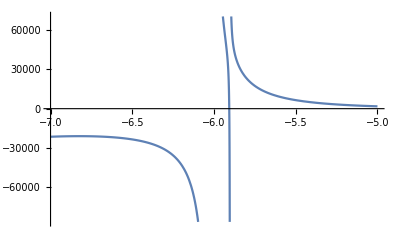

```mathematica
Plot[Ev[x],{x,-7,-5}]
```